```mathematica
f[x_,c_] := x^2+c
```

```mathematica
Plot3D[{f[x,1]f[y,1],f[x,0]f[y,0],f[x,-1]f[y,-1]},{x,-2,2},{y,-2,2},PlotRange->{-2,4},PlotPoints->50]
```

-Graphics3D-

```mathematica
Plot3D[{D[f[x0,-1]f[y,-1],x0]/.x0->x,D[f[x,-1]f[y0,-1],y0]/.y0->y,0},{x,-2,2},{y,-2,2},PlotPoints->50]
```

-Graphics3D-

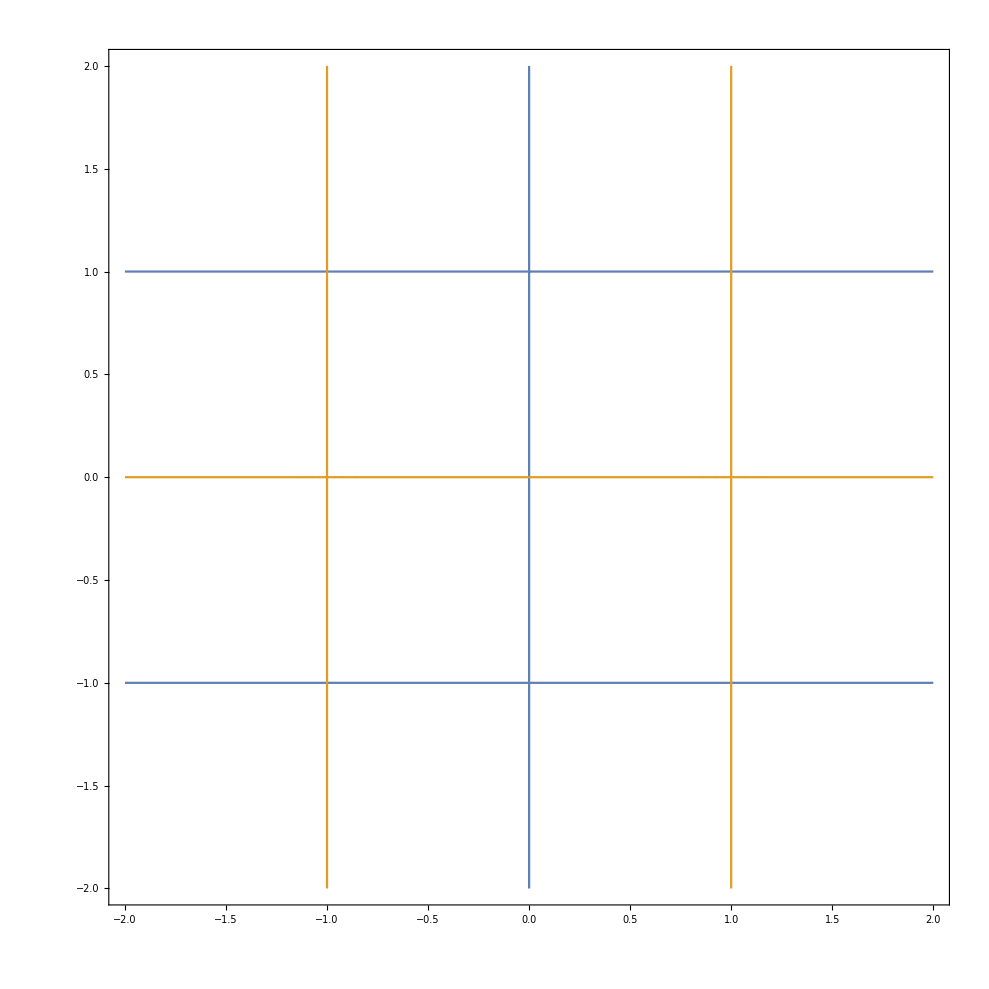

```mathematica
ContourPlot[{D[f[x0,-1]f[y,-1],x0]/.x0->x,D[f[x,-1]f[y0,-1],y0]/.y0->y},{x,-2,2},{y,-2,2}]
```

```mathematica
g[x_]:=(x-2)x(x+2)
```

```mathematica
Plot3D[g[x]g[y],{x,-2.5,2.5},{y,-2.5,2.5},PlotRange->{-10,10},PlotPoints->50]
```

-Graphics3D-

```mathematica
Plot3D[{D[g[x0]g[y],x0]/.x0->x,D[g[x]g[y0],y0]/.y0->y,0},{x,-2.5,2.5},{y,-2.5,2.5},PlotPoints->50]
```

-Graphics3D-

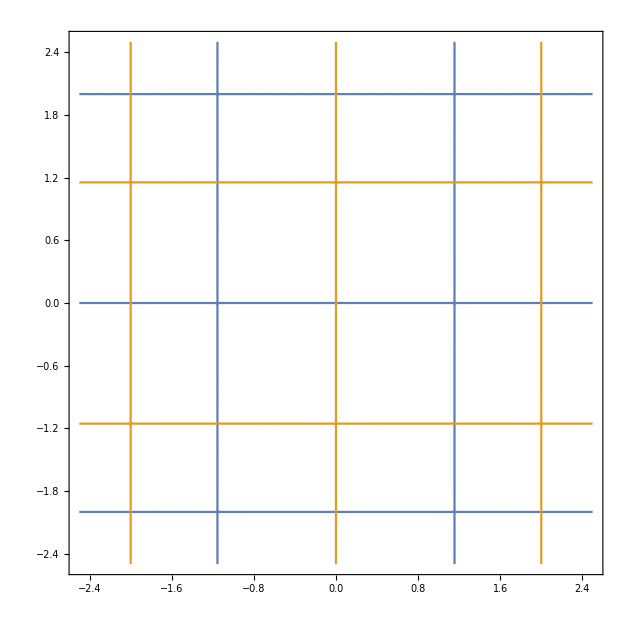

```mathematica
ContourPlot[{D[g[x0]g[y],x0]/.x0->x,D[g[x]g[y0],y0]/.y0->y},{x,-2.5,2.5},{y,-2.5,2.5},PlotPoints->50]
```

```mathematica
h[x_,y_]:=17x y-3 x^3 y-5x y^3+x^3 y^3-x y^2+1/2x^2y
```

```mathematica
Plot3D[h[x,y],{x,-3,3},{y,-3,3},PlotRange->{-20,20},PlotPoints->50]
```

-Graphics3D-

```mathematica
Plot3D[{D[h[x0,y],x0]/.x0->x,D[h[x,y0],y0]/.y0->y,0},{x,-2.5,2.5},{y,-2.5,2.5},PlotPoints->50]
```

-Graphics3D-

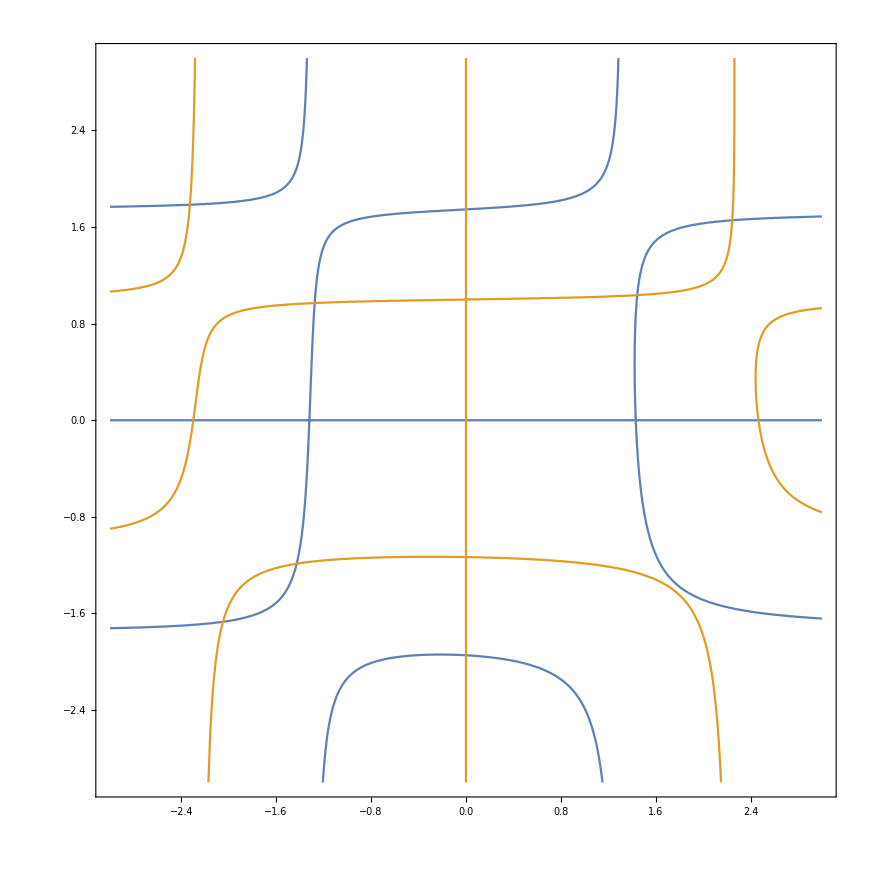

```mathematica
ContourPlot[{D[h[x0,y],x0]/.x0->x,D[h[x,y0],y0]/.y0->y},{x,-3,3},{y,-3,3},PlotPoints->50]
```